# Sensitivities of Factorizations

Throughout Q is orthogonal, W is skew, D is diagonal and T is pseudo upper triangular.  The goal is to be able to compute the sensitivities of the outputs of the factorization in terms of the factorization and the derivative of the input.

## LU Decomposition

Given A and A' compute L, U,  L', and U' with fixed pivot order p 
	A⟦p⟧=L.U ⟹A'=L'.U+L.U'
This is a system of m×m equations in the (m(m-1))/2 non-zero entries in L' (the derivative of the constant diagonal entries are zero) and the the (m(m+1))/2 non-zero entries in U'.  It is a square system.  
	L^-1 A' U^-1=L^-1.L'+U'.U^-1
This is a structural decomposition with L^-1.L strictly lower triangular and U'.U upper triangular.

This is easily computable.

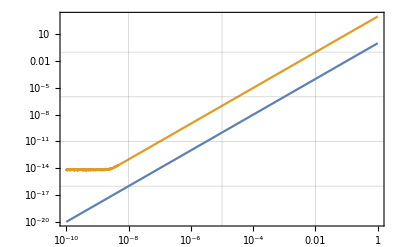

```mathematica
m=56;
{A,Ad}=RandomReal[{-1,1},{2,m,m}];
{LU,p,c}=LUDecomposition[A];
{A,Ad}={A⟦p⟧,Ad⟦p⟧};
U=UpperTriangularize[LU];
L=LU-U+IdentityMatrix[m];
LInvAdUInv=Inverse[L].Ad.Inverse[U];
Ld=L.LowerTriangularize[LInvAdUInv,-1];
Ud=UpperTriangularize[LInvAdUInv].U;
f[h_]:=Norm[A+h Ad -(L +h Ld).(U+h Ud)]
LogLogPlot[{h^2,f[h]},{h, 10^-10, 1},
Frame->True,
GridLines->Automatic]
```

There is another way to compute this using the Kronecker product.

## QR Decomposition

Task: Given A and A' compute Q, R,  Q', and R'.    Note I can only use Q=ⅇ^W if Q is square.

Assume A∈ℝ^(m×m) is square then
 
A=Q.R ⟹A'=Q'.R+Q.R'⟹Qᵀ.A'=Qᵀ.Q'.R+R'⟹Qᵀ.A'=W.R+R'

This is a set of m×m equations (each entry of the matrix) in the (m(m-1))/2 independent entries of the skew matrix W=Qᵀ.Q' and the (m(m+1))/2 non-zero entries of the upper triangular matrix R'.  
	Qᵀ.A'=W.R+R'⟹Qᵀ.A'.R^-1=W+R'.R^-1
This is also a structural decomposition since R'.R^-1 is upper triangular and W is skew. Form Qᵀ.A'.R^-1 and extract the strictly lower triangular portion. Define W by mirroring this portion in the upper triangular portion. Compute R'.R^-1 by subtracting W from Qᵀ.A'.R^-1 and finally reconstruct R'  by multiplying by R.

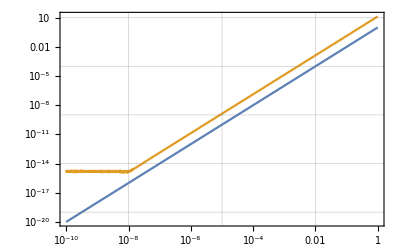

```mathematica
m=12;
{A,Ad}=RandomReal[{-1,1},{2,m,m}];
{Qt,R}=QRDecomposition[A];Q=Qtᵀ;
QtAdRInv=Qt.Ad.Inverse[R];
W=LowerTriangularize[QtAdRInv,-1];W-=Wᵀ;
Rd=(QtAdRInv-W).R;
f[h_]:= Norm[A+h Ad -Q.(IdentityMatrix[n]+h W).(R+ h Rd)]
LogLogPlot[{h^2,f[h]},{h, 10^-10, 1},
Frame->True,
GridLines->Automatic]
```

## Eigenvalue Decomposition: A=Aᵀ

Task: Given A and A' compute D, Q, D', and Q'.  
	A=Q.D.Qᵀ⟹A'=Q'.D.Qᵀ+Q.D'.Qᵀ+Q.D.Q'ᵀ
so if W=Qᵀ.Q' then 
	Qᵀ.A'.Q=Qᵀ.Q'.D+D'+D.Q'ᵀ.Q=W.D+D'-W.D
and W is skew.  This looks like a set of m^2 equations in m unknowns (from the diagonal D') and (m(m-1))/2 unknowns in the skew matrix W.  However since A=Aᵀ we have A'ᵀ=A' and we only need the top (or bottom) half and the diagonal of the matrix equations.

Since W is skew and D is diagonal W.D and D.W have zero diagonal entries. As a result
	D'=diagonal(Qᵀ.A'.Q)
and we are left with the matrix equations
	B=W.D-W.D
where B=Qᵀ.A'.Q-diagonal(Qᵀ.A'.Q).  The solution of this can be written simply as 
	W=K∘B
where K_ij={0 | if | i=j
1/(D_jj-D_ii) | if | i≠j

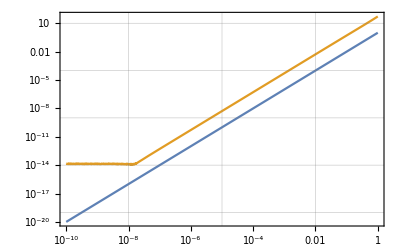

```mathematica
m=12;
{A,Ad}=RandomReal[{-1,1},{2,m,m}];{A,Ad}={A+Aᵀ,Ad+Adᵀ};
{λ,Qt}=Eigensystem[A];Q=Qtᵀ;
Λ=DiagonalMatrix[λ];
QtAdQ=Qᵀ.Ad.Q;
λd=Diagonal[QtAdQ];
Id=IdentityMatrix[m];
B=QtAdQ-DiagonalMatrix[λd];
K=Table[
If[i==j,0, 1/(λ⟦j⟧-λ⟦i⟧)],{i,m},{j,m}];
W=K*B;
f[h_]:= Norm[A+h Ad - Q.(Id+h W).DiagonalMatrix[λ+h λd].(Id - h W).Qᵀ]
LogLogPlot[{h^2,f[h]},{h, 10^-10, 1},
Frame->True,
GridLines->Automatic]
```

## Eigenvalue Decomposition: A≠Aᵀ

Task: Given A and A' compute D, X, D', and X'.  
	A=X.D.X^-1⟹A'=X'.D.X^-1+X.D'.X^-1-X.D.X^-2.X'
Noting that X.X^-1=Id ⟹X'.X^-1-X.X^-2.X'=0 which is the same as X'.X^-1=X^-1.X' which is the same as 
	X.X'=X'.X
in other words X' commutes with X so 
	A'=X'.D.X^-1+X.D'.X^-1-X.D.X'.X^-2
which gives
	X^-1.A'.X=X^-1.X'.D+D'-D.X'.X^-1
defining Y=X^-1.X'=X'.X^-1 and B=X^-1.A'.X we have 
	B=Y.D+D'-D.Y
The diagonal entries of D.Y and Y.D are equal since D is diagonal.  As a result we have
	D'=DiagonalMatrix[Diagonal[B]]
and the remaining portions of the equation are solvable just like before using the K matrix. 
The last step is to recreate X'=X.Y

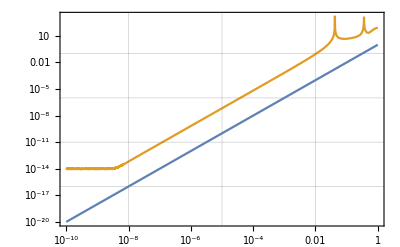

```mathematica
m=12;
{A,Ad}=RandomReal[{-1,1},{2,m,m}];
{λ,Xt}=Eigensystem[A];X=Xtᵀ;
Λ=DiagonalMatrix[λ];
XInvAdX=Inverse[X].Ad.X;
λd=Diagonal[XInvAdX];
Id=IdentityMatrix[m];
B=XInvAdX-DiagonalMatrix[λd];
K=Table[
If[i==j,0, 1/(λ⟦j⟧-λ⟦i⟧)],{i,m},{j,m}];
Y=K*B;
Xd =X.Y; 
f[h_]:= Norm[A+h Ad -(X+h Xd).DiagonalMatrix[λ+h λd].Inverse[(X+h Xd)]]
LogLogPlot[{h^2,f[h]},{h, 10^-10, 1},
Frame->True,
GridLines->Automatic]
```

Other better formulations of this work as well.  You can avoid folding the X into the Y

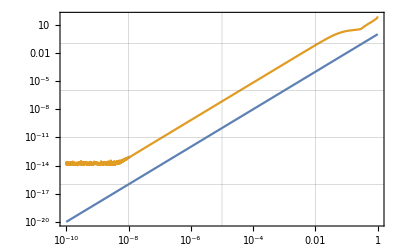

```mathematica
m=12;
{A,Ad}=RandomReal[{-1,1},{2,m,m}];
{λ,Xt}=Eigensystem[A];X=Xtᵀ;
Λ=DiagonalMatrix[λ];
XInvAdX=Inverse[X].Ad.X;
λd=Diagonal[XInvAdX];
Id=IdentityMatrix[m];
B=XInvAdX-DiagonalMatrix[λd];
K=Table[
If[i==j,0, 1/(λ⟦j⟧-λ⟦i⟧)],{i,m},{j,m}];
Y=K*B;
Xd =X.Y; 
f[h_]:= Norm[A+h Ad -X.(Id+h Y).DiagonalMatrix[λ+h λd].Inverse[Id+ h Y].Inverse[X]]
LogLogPlot[{h^2,f[h]},{h, 10^-10, 1},
Frame->True,
GridLines->Automatic]
```

Other better formulations of this work as well.  You can avoid folding the X into the Y. You can also avoid the internal inverse computation since (I+h Y)^-1=I-h Y+h^2 Y.Y-

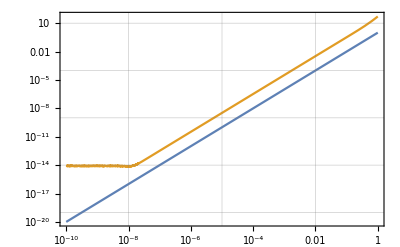

```mathematica
m=12;
{A,Ad}=RandomReal[{-1,1},{2,m,m}];
{λ,Xt}=Eigensystem[A];X=Xtᵀ;
Λ=DiagonalMatrix[λ];
XInvAdX=Inverse[X].Ad.X;
λd=Diagonal[XInvAdX];
Id=IdentityMatrix[m];
B=XInvAdX-DiagonalMatrix[λd];
K=Table[
If[i==j,0, 1/(λ⟦j⟧-λ⟦i⟧)],{i,m},{j,m}];
Y=K*B;
Xd =X.Y; 
f[h_]:= Norm[A+h Ad -X.(Id+h Y).DiagonalMatrix[λ+h λd].(Id- h Y).Inverse[X]]
LogLogPlot[{h^2,f[h]},{h, 10^-10, 1},
Frame->True,
GridLines->Automatic]
```

## SVD: A=U.S.Vᵀ

Task: Given A and A' compute U,S,V, and U', S',V'.   This is explicitly a thin SVD. 
	A=U.S.Vᵀ⟹A'=U'.S.Vᵀ+U.S'.Vᵀ+U.S.V'ᵀ
so 
	Uᵀ.A'.V=Uᵀ.U'.S+S'+S.V'ᵀ.V
defining the skew matrices X=Uᵀ.U' and Y=Vᵀ.V' and B=Uᵀ.A'.V we have
	B=X.S+S'-S.Y
since X and Y are skew they have zeros on the diagonal.  Multiplying the the diagonal matrix S does not change that.

A=X.D.X^-1⟹A'=X'.D.X^-1+X.D'.X^-1-X.D.X^-2.X'
Noting that X.X^-1=Id ⟹X'.X^-1-X.X^-2.X'=0 which is the same as X'.X^-1=X^-1.X' which is the same as 
	X.X'=X'.X
in other words X' commutes with X so 
	A'=X'.D.X^-1+X.D'.X^-1-X.D.X'.X^-2
which gives
	X^-1.A'.X=X^-1.X'.D+D'-D.X'.X^-1
defining Y=X^-1.X'=X'.X^-1 and B=X^-1.A'.X we have 
	B=Y.D+D'-D.Y
The diagonal entries of D.Y and Y.D are equal since D is diagonal.  As a result we have
	D'=DiagonalMatrix[Diagonal[B]]
and the remaining portions of the equation are solvable just like before using the K matrix. 
The last step is to recreate X'=X.Y

```mathematica
m=12;
{A,Ad}=RandomReal[{-1,1},{2,m,m}];
{λ,Xt}=Eigensystem[A];X=Xtᵀ;
Λ=DiagonalMatrix[λ];
XInvAdX=Inverse[X].Ad.X;
λd=Diagonal[XInvAdX];
Id=IdentityMatrix[m];
B=XInvAdX-DiagonalMatrix[λd];
K=Table[
If[i==j,0, 1/(λ⟦j⟧-λ⟦i⟧)],{i,m},{j,m}];
Y=K*B;
Xd =X.Y; 
f[h_]:= Norm[A+h Ad -(X+h Xd).DiagonalMatrix[λ+h λd].Inverse[(X+h Xd)]]
LogLogPlot[{h^2,f[h]},{h, 10^-10, 1},
Frame->True,
GridLines->Automatic]
```

-Graphics-

Other better formulations of this work as well.  You can avoid folding the X into the Y

```mathematica
m=12;
{A,Ad}=RandomReal[{-1,1},{2,m,m}];
{λ,Xt}=Eigensystem[A];X=Xtᵀ;
Λ=DiagonalMatrix[λ];
XInvAdX=Inverse[X].Ad.X;
λd=Diagonal[XInvAdX];
Id=IdentityMatrix[m];
B=XInvAdX-DiagonalMatrix[λd];
K=Table[
If[i==j,0, 1/(λ⟦j⟧-λ⟦i⟧)],{i,m},{j,m}];
Y=K*B;
Xd =X.Y; 
f[h_]:= Norm[A+h Ad -X.(Id+h Y).DiagonalMatrix[λ+h λd].Inverse[Id+ h Y].Inverse[X]]
LogLogPlot[{h^2,f[h]},{h, 10^-10, 1},
Frame->True,
GridLines->Automatic]
```

-Graphics-

Other better formulations of this work as well.  You can avoid folding the X into the Y. You can also avoid the internal inverse computation since (I+h Y)^-1=I-h Y+h^2 Y.Y-

```mathematica
m=12;
{A,Ad}=RandomReal[{-1,1},{2,m,m}];
{λ,Xt}=Eigensystem[A];X=Xtᵀ;
Λ=DiagonalMatrix[λ];
XInvAdX=Inverse[X].Ad.X;
λd=Diagonal[XInvAdX];
Id=IdentityMatrix[m];
B=XInvAdX-DiagonalMatrix[λd];
K=Table[
If[i==j,0, 1/(λ⟦j⟧-λ⟦i⟧)],{i,m},{j,m}];
Y=K*B;
Xd =X.Y; 
f[h_]:= Norm[A+h Ad -X.(Id+h Y).DiagonalMatrix[λ+h λd].(Id- h Y).Inverse[X]]
LogLogPlot[{h^2,f[h]},{h, 10^-10, 1},
Frame->True,
GridLines->Automatic]
```

-Graphics-